```mathematica
nGrid = 10+1; Δy=1/(nGrid-1);
y = Table[(i-1)Δy,{i,1,nGrid}];
u=Array["u",nGrid];
```

```mathematica
discreteEqns = Table[u[[i+1]]-2u[[i]]+u[[i-1]]==0,{i,2,nGrid-1}]
```

{u[1]-2 u[2]+u[3]==0,u[2]-2 u[3]+u[4]==0,u[3]-2 u[4]+u[5]==0,u[4]-2 u[5]+u[6]==0,u[5]-2 u[6]+u[7]==0,u[6]-2 u[7]+u[8]==0,u[7]-2 u[8]+u[9]==0,u[8]-2 u[9]+u[10]==0,u[9]-2 u[10]+u[11]==0}

```mathematica
bcs = {u[[1]]==0, u[[nGrid]]==1}
```

{u[1]==0,u[11]==1}

```mathematica
eqns = Join[discreteEqns,bcs]
```

{u[1]-2 u[2]+u[3]==0,u[2]-2 u[3]+u[4]==0,u[3]-2 u[4]+u[5]==0,u[4]-2 u[5]+u[6]==0,u[5]-2 u[6]+u[7]==0,u[6]-2 u[7]+u[8]==0,u[7]-2 u[8]+u[9]==0,u[8]-2 u[9]+u[10]==0,u[9]-2 u[10]+u[11]==0,u[1]==0,u[11]==1}

```mathematica
sol = Solve[eqns,u]
```

{{u[1]→0,u[2]→1/10,u[3]→1/5,u[4]→3/10,u[5]→2/5,u[6]→1/2,u[7]→3/5,u[8]→7/10,u[9]→4/5,u[10]→9/10,u[11]→1}}

```mathematica
uVals=u/.sol
```

{{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}}

```mathematica
data=Table[{y[[i]],uVals[[1]][[i]]},{i,nGrid}]
```

{{0,0},{1/10,1/10},{1/5,1/5},{3/10,3/10},{2/5,2/5},{1/2,1/2},{3/5,3/5},{7/10,7/10},{4/5,4/5},{9/10,9/10},{1,1}}

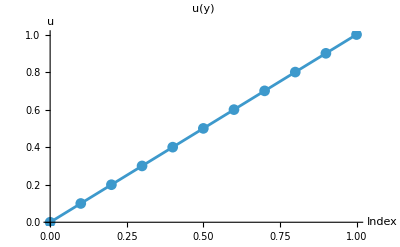

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,AxesLabel->{"Index","u"},PlotLabel->"u(y)"]
```

```mathematica
A
```